# Versuch B20

```mathematica
ClearAll["Global`*"]
```

## 2.1

### 2.1.1

```mathematica
D[d/4(1-(2g/d-1)^2),d]//Simplify
D[d/4(1-(2g/d-1)^2),g]//Simplify
```

g^2/d^2

1-(2 g)/d

```mathematica
d=146.8-17
Δd=Sqrt[2*(0.1)^2]
```

129.8

0.141421

```mathematica
tab1={41.6,41.8,41.7,41.5,41.5,41.4};
xlinse=Mean[tab1]
```

41.5833

```mathematica
g=xlinse-17
```

24.5833

```mathematica
Δg=Sqrt[(0.1/Sqrt[6])^2+0.1^2]
```

0.108012

```mathematica
fbest1=d/4(1-(2g/d-1)^2)
```

19.9274

```mathematica
d/2(1-Sqrt[1-4fbest1/d])
d/2(1+Sqrt[1-4f/d])
```

24.5833

64.9 (1+√(1-0.0308166 f))

```mathematica
Δfbest1= Sqrt[g^4/d^4(Sqrt[2]*0.1)^2+(1-2g/d)^2(Δg)^2]
```

0.0672901

### 2.1.2

```mathematica
tab2={37.4,37.0,37.0,36.7,36.7,36.6}
```

{37.4,37.,37.,36.7,36.7,36.6}

```mathematica
Mean[tab2]
```

36.9

```mathematica
0.1/Sqrt[6]
```

0.0408248

```mathematica
fbest2=36.9-17
```

19.9

```mathematica
Δfbest2=Sqrt[(0.1/Sqrt[6])^2 + 0.1^2]
```

0.108012

### 2.1.3

```mathematica
w1=1/Δfbest1^2
w2=1/Δfbest2^2
```

220.85

85.7143

```mathematica
fbest=(w1 fbest1+w2 fbest2)/(w1+w2)
```

19.9197

```mathematica
Δfbest=1/Sqrt[w1+w2]
```

0.0571135

## 2.2

```mathematica
tab3={55.3,55.0,54.7,55.4,54.8,55.1}
```

{55.3,55.,54.7,55.4,54.8,55.1}

```mathematica
Mean[tab3]
```

55.05

```mathematica
fsystem=Mean[tab3]-17
```

38.05

```mathematica
Δfsystem=Δfbest2
```

0.108012

```mathematica
1/(1/fsystem-1/fbest)
```

-41.8056

```mathematica
1/(1/fs-1/fb)//Simplify
```

(fb fs)/(fb-fs)

```mathematica
D[(fb fs)/(fb-fs),fb]//Simplify
D[(fb fs)/(fb-fs),fs]//Simplify
```

-fs^2/(fb-fs)^2

fb^2/(fb-fs)^2

```mathematica
Simplify[√((fs^2/(fb-fs)^2)^2 Δfb^2+(fb^2/(fb-fs)^2)^2 Δfs^2),fb>0&&fs>0]
```

(√(fs^4 Δfb^2+fb^4 Δfs^2))/(fb-fs)^2

```mathematica
f2=(fbest fsystem)/(fbest-fsystem)
```

-41.8056

```mathematica
Δf2=(√(fsystem^4 Δfbest^2+fbest^4 Δfsystem^2))/(fbest-fsystem)^2
```

0.283342

## 3.3

```mathematica
tab41={30.3,30.2,30.2};
tab42={56.4,55.9,56.4};
Mean[tab41]
Mean[tab42]
0.1/Sqrt[3]
```

30.2333

56.2333

0.057735

```mathematica
Sqrt[(0.1/Sqrt[3])^2 + 0.1^2]
```

0.11547

```mathematica
g1=Mean[tab41]-17
g2=Mean[tab42]-17
```

13.2333

39.2333

```mathematica
s=(g1+g2)
```

52.4667

```mathematica
Δs=Sqrt[(0.1/Sqrt[3])^2 + 0.1^2+(0.1/Sqrt[3])^2 + 0.1^2]
```

0.163299

```mathematica
0.1/Sqrt[6]
```

0.0408248

```mathematica
tab43={63.6,63.7,63.6}
tab44={121.9,122.2,121.9}
Mean[tab43]
Mean[tab44]
```

{63.6,63.7,63.6}

{121.9,122.2,121.9}

63.6333

122.

```mathematica
Mean[tab43]-17
Mean[tab44]-17
```

46.6333

105.

```mathematica
z1=Mean[tab43]
z2=Mean[tab44]
```

63.6333

122.

```mathematica
Δ=Mean[tab44]-Mean[tab43]
```

58.3667

```mathematica
√((0.1/(√3))^2+(0.1/(√3))^2)
```

0.0816497

```mathematica
d=144.7-17
```

127.7

```mathematica
Δd=Sqrt[2]*0.1
```

0.141421

```mathematica
(d^2-Δ^2)/(4d)
```

25.2557

```mathematica
fbessel=1/2Sqrt[(d-s)^2-Δ^2]
```

23.7349

```mathematica
(d-s)^2-Δ^2
```

2253.39

```mathematica
d
s
Δ
```

127.7

52.4667

58.3667

```mathematica
1/2Sqrt[(d-s)^2-Δ^2]
```

23.7349

```mathematica
Δfbessel=((d-s)/(2 √((d-s)^2-Δ^2)))^2 Δd^2+((d-s)/(2 √((d-s)^2-Δ^2)))^2 Δs^2+(Δ/(2 √((d-s)^2-Δ^2)))^2 √((0.1/(√3))^2+(0.1/(√3))^2)
```

0.0601638

```mathematica
h=s-2fbessel
Δh=Sqrt[(Δs)^2+2(Δfbessel)^2]
```

4.99682

0.184136

```mathematica
D[1/2Sqrt[(es-ss)^2-Δss^2],{{es,ss,Δss}}]
```

{(es-ss)/(2 √((es-ss)^2-Δss^2)),-(es-ss)/(2 √((es-ss)^2-Δss^2)),-Δss/(2 √((es-ss)^2-Δss^2))}

```mathematica
Module[{d,s,Δ},D[1/2Sqrt[(d-s)^2-Δ^2],{{d,s,Δ}}]]
```

{(d$4123-s$4123)/(2 √((d$4123-s$4123)^2-Δ$4123^2)),-(d$4123-s$4123)/(2 √((d$4123-s$4123)^2-Δ$4123^2)),-Δ$4123/(2 √((d$4123-s$4123)^2-Δ$4123^2))}

```mathematica
Sqrt[2]*0.1
```

0.141421

### Computation of distances

```mathematica
z1p=z1-17
z2p=z2-17
```

46.6333

105.

```mathematica
Δzp=Sqrt[(0.1/Sqrt[3])^2+0.1^2]
```

0.11547

```mathematica
L1H1=1/2(15+d-h-2 z1p-Δ)
L2H2=1/2(-15+d+h-2 z2p+ Δ)
```

-6.96507

-16.9683

```mathematica
fbessel-L1H1+15+L2H2+fbessel
```

52.4667

```mathematica
52.466666666666654/28
```

1.87381

```mathematica
28*2.5
```

70.

```mathematica
h
```

4.99682

```mathematica
fbessel/2
(fbessel-L1H1)/2
(fbessel-L1H1+15)/2
(fbessel-L1H1+15+L2H2)/2
(fbessel-L1H1+15+L2H2+fbessel)/2
```

11.8675

15.35

22.85

14.3659

26.2333

```mathematica
Δd
```

0.141421

```mathematica
Δh
```

0.184136

```mathematica
Δz1=0.1/Sqrt[3]
```

0.057735

```mathematica
1/2 Sqrt[Δd^2+Δh^2+2*Δzp^2]
```

0.141927

### Vergleich

```mathematica
fval=-fbest f2/(15-fbest-f2)
```

-(f2 fbest)/(15-f2-fbest)

```mathematica
1/(1/fbest+1/f2-15/(fbest f2))
```

1/(1/f2+1/fbest-15/(f2 fbest))

```mathematica
hval=15^2/(15-fbest-f2)
```

225/(15-f2-fbest)

```mathematica
δ=15;
```

```mathematica
(√(f2^2 (f2-δ)^2 Δfbest^2+fbest^2 (fbest-δ)^2 Δf2^2))/(δ-fbest-f2)^2
```

(√((-15+fbest)^2 fbest^2 Δf2^2+(-15+f2)^2 f2^2 Δfbest^2))/(15-f2-fbest)^2

```mathematica
√(((f2 (-δ+f2))/(-δ+fbest+f2)^2)^2 Δfbest^2+((fbest (-δ+fbest))/(-δ+fbest+f2)^2)^2 Δf2^2)
```

√(((-15+fbest)^2 fbest^2 Δf2^2)/(-15+f2+fbest)^4+((-15+f2)^2 f2^2 Δfbest^2)/(-15+f2+fbest)^4)

```mathematica
Solve[{1/2Sqrt[(d-ss)^2-Δ^2]==fval},{ss}]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ss→0.0111111 (11493.-1. √(2.7594×10^7+32400. fbest^2-(7.29×10^6 fbest^2)/(225.-30. f2+f2^2-30. fbest+2. f2 fbest+fbest^2)+(972000. f2 fbest^2)/(225.-30. f2+f2^2-30. fbest+2. f2 fbest+fbest^2)+(972000. fbest^3)/(225.-30. f2+f2^2-30. fbest+2. f2 fbest+fbest^2)-(64800. f2 fbest^3)/(225.-30. f2+f2^2-30. fbest+2. f2 fbest+fbest^2)-(32400. fbest^4)/(225.-30. f2+f2^2-30. fbest+2. f2 fbest+fbest^2)))},{ss→0.0111111 (11493.+√(2.7594×10^7+32400. fbest^2-(7.29×10^6 fbest^2)/(225.-30. f2+f2^2-30. fbest+2. f2 fbest+fbest^2)+(972000. f2 fbest^2)/(225.-30. f2+f2^2-30. fbest+2. f2 fbest+fbest^2)+(972000. fbest^3)/(225.-30. f2+f2^2-30. fbest+2. f2 fbest+fbest^2)-(64800. f2 fbest^3)/(225.-30. f2+f2^2-30. fbest+2. f2 fbest+fbest^2)-(32400. fbest^4)/(225.-30. f2+f2^2-30. fbest+2. f2 fbest+fbest^2)))}}

```mathematica
Δh=δ^2/(δ-fbest-f2)^2 Sqrt[Δfbest^2 + Δf2^2]
```

(225 √(Δf2^2+Δfbest^2))/(15-f2-fbest)^2

```mathematica
{{g->1/2 (e-h-Δ),b->1/2 (e-h+Δ),L1H1->1/2 (d+e-h-2 z1-Δ),L2H2->1/2 (-d+e+h-2 z2+Δ)}}
```

{{g→1/2 (-63.3635+e),b→1/2 (53.3699+e),-23.9651→1/2 (-62.9301+e),-33.9683→1/2 (-308.337+e)}}

```mathematica
d
```

127.7

```mathematica
1/2 Sqrt[(Sqrt[2/3]*0.1)^2 + (Δh)^2 + (0.1/Sqrt[3])^2 + (0.1/Sqrt[3])^2]
```

1/2 √(0.0133333+(50625 (Δf2^2+Δfbest^2))/(15-f2-fbest)^4)

```mathematica
1/2 (15+d-hval-2 z1-Δ)
1/2 (-15+d+hval-2 z2+Δ)
```

1/2 (-42.9333-225/(15-f2-fbest))

1/2 (-72.9333+225/(15-f2-fbest))

```mathematica
L1H1=1/2(15+d-hval-z1-z2)
L2H2=1/2(d-15+hval-z1-z2)
```

1/2 (-42.9333-225/(15-f2-fbest))

1/2 (-72.9333+225/(15-f2-fbest))

```mathematica
{{g->1/2 (e-h-Δ),b->1/2 (e-h+Δ),L1H1->1/2 (15+e-h-2 z1-Δ),L2H2->1/2 (-15+e+h-2 z2+Δ)}}
```

{{g→1/2 (-63.3635+e),b→1/2 (53.3699+e),1/2 (-42.9333-225/(15-f2-fbest))→1/2 (-175.63+e),1/2 (-72.9333+225/(15-f2-fbest))→1/2 (-195.637+e)}}

```mathematica
fval+15+fval
```

15-(2 f2 fbest)/(15-f2-fbest)

```mathematica
fval/4
```

-(f2 fbest)/(4 (15-f2-fbest))

```mathematica
(fval-L1H1)/4
```

1/4 (1/2 (42.9333+225/(15-f2-fbest))-(f2 fbest)/(15-f2-fbest))

```mathematica
(fval-L1H1+15)/4
```

1/4 (15+1/2 (42.9333+225/(15-f2-fbest))-(f2 fbest)/(15-f2-fbest))

```mathematica
(fval-L1H1+15+L2H2)/4
```

1/4 (15+1/2 (-72.9333+225/(15-f2-fbest))+1/2 (42.9333+225/(15-f2-fbest))-(f2 fbest)/(15-f2-fbest))

```mathematica
(fval+hval+fval)/4
```

1/4 (225/(15-f2-fbest)-(2 f2 fbest)/(15-f2-fbest))

## 2.4

```mathematica
tab5={48.6,48.4,48.4,48.5}
```

{48.6,48.4,48.4,48.5}

```mathematica
Mean[tab5]
```

48.475

```mathematica
0.1/Sqrt[4]
```

0.05

```mathematica
48.475-17
```

31.475

```mathematica
((0.1/Sqrt[4])^2 + 0.1^2)//Sqrt
```

0.111803

```mathematica
Mean[{116.1,116.5,116}]
```

116.2

```mathematica
Mean[{116.9,116.3,116.7}]
```

116.633

```mathematica
((0.1/Sqrt[3])^2+(0.1/Sqrt[3])^2)//Sqrt
```

0.0816497

### Spherical Abberation

```mathematica
tab6=ToExpression/@Import[NotebookDirectory[]<>"data1.csv"];
midtab6=Mean/@Transpose[tab6]
```

{27.8,25.5333,24.9333,24.4333,22.9333}

```mathematica
tab7=ToExpression/@Import[NotebookDirectory[]<>"data2.csv"];
midtab7=Mean/@Transpose[tab7]
```

{32.3667,29.4333,25.2333,22.6}

```mathematica
0.1/Sqrt[3]
```

0.057735

```mathematica
blenderadius={16,24,32,40};
```

```mathematica
difftab6=(midtab6[[1]]-#)&/@midtab6
```

{0.,2.26667,2.86667,3.36667,4.86667}

```mathematica
((0.1/Sqrt[3])^2+(0.1/Sqrt[3])^2)//Sqrt
```

0.0816497

```mathematica
Sqrt[2]0.1/Sqrt[3]
```

0.0816497

```mathematica
difftab7=(midtab7[[1]]-#)&/@midtab7
```

{0.,2.93333,7.13333,9.76667}

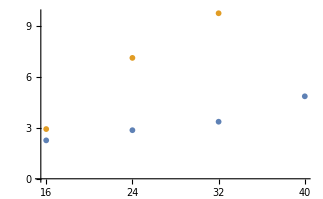

```mathematica
ListPlot[{Transpose[{blenderadius,difftab6[[2;;]]}],Transpose[{blenderadius[[1;;-2]],difftab7[[2;;]]}]}]
```

```mathematica
difftab6*20
```

{0.,45.3333,57.3333,67.3333,97.3333}

```mathematica
Sqrt[2]0.1/Sqrt[3]*20
```

1.63299

```mathematica
difftab7*20
```

{0.,58.6667,142.667,195.333}

```mathematica
sphfit1=LinearModelFit[Transpose[{blenderadius,difftab6[[2;;]]}],x,x]
```

FittedModel[0.436667+0.10375 x]

```mathematica
sphfit2=LinearModelFit[Transpose[{blenderadius[[1;;-2]],difftab7[[2;;]]}],x,x]
```

FittedModel[-3.63889+0.427083 x]

```mathematica
sphfit1[4]*20
sphfit1[40]*20
```

17.0333

91.7333

```mathematica
Solve[sphfit2[x]==0,x]
Solve[sphfit2[x]==12,x]
```

{{x→8.52033}}

{{x→36.6179}}

```mathematica
(8.52032520325204-4)*5
(36.61788617886178-4)*5
```

22.6016

163.089

### 2.5.3 Astigmatismus

```mathematica
tab8={30.8,31.0,30.5}
tab9={29.5,29.7,29.5}
```

{30.8,31.,30.5}

{29.5,29.7,29.5}

```mathematica
Mean[tab8]
Mean[tab9]
```

30.7667

29.5667

```mathematica
0.1/Sqrt[3]//N
```

0.057735

```mathematica
Mean[tab8]-Mean[tab9]
```

1.2

```mathematica
Sqrt[(0.1/Sqrt[3])^2+(0.1/Sqrt[3])^2]
```

0.0816497